```mathematica
𝒫[n_]:= 2/(n^(1/3)3^(2/3)Gamma[1/3]^2)
```

```mathematica
𝒫[2]//N
```

0.106336

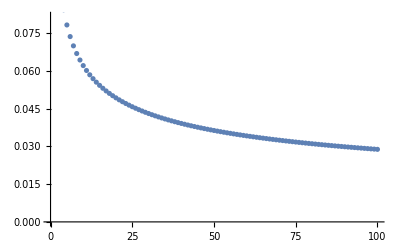

```mathematica
ListPlot[Table[𝒫[n], {n, 1, 100}]]
```

```mathematica
𝒫a[n_]:= 1/(2π)∫_0^∞ ⅇ^((2n+1)(x-1/2 Sinh[2x]))ⅆx
```

```mathematica
𝒫a[0]
```

(ⅇ^(-ⅈ/2) (1-ⅇ^ⅈ (-1+Erf[1/2+ⅈ/2])+ⅈ Erfi[1/2+ⅈ/2]))/(4 √π)

```mathematica
N[(ⅇ^(-ⅈ/2) (1-ⅇ^ⅈ (-1+Erf[1/2+ⅈ/2])+ⅈ Erfi[1/2+ⅈ/2]))/(4 √π)]
```

0.150401-1.38778×10^-17 ⅈ

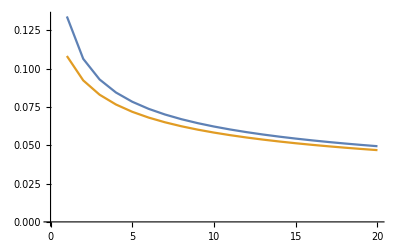

```mathematica
ListLinePlot[{Table[𝒫[n], {n, 1, 20}], Table[𝒫a[n], {n, 1, 20}]}]
```

```mathematica
Table[1/6 i, {i, 0,10}]//N
```

{0.,0.166667,0.333333,0.5,0.666667,0.833333,1.,1.16667,1.33333,1.5,1.66667}